### Rotate to Jx=0,Jy=0 coordinates 21/03/2015

```mathematica
η[x_]:={(x α (-1+α+α^2)-√(x^2 α^2+c^2 (-1+α^2)))/(-1+α^2),(x α (-1+α+α^2)+√(x^2 α^2+c^2 (-1+α^2)))/(-1+α^2)}
```

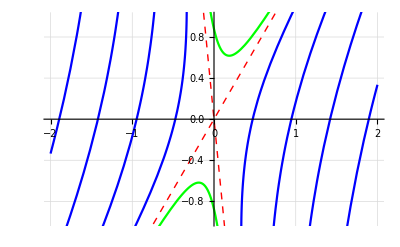

```mathematica
xmax=2.0;ηmax=1.0;
αval=0.9;
dc=1/6 xmax/(√(1/αval^2-1));
cval=Table[i,{i,dc,5*dc,dc}];
Show[
Plot[
{η[x]}/.{α->αval,c->cval}//Evaluate,
{x,-xmax,xmax},
PlotStyle->Blue,
GridLines->Automatic],
Plot[
{η[x]}/.{α->αval,c->0.5/αval ⅈ cval}//Evaluate,
{x,-xmax,xmax},
PlotStyle->Green],
Plot[{α^2/(α-1)x,(α(α+2))/(α+1)x}/.α->αval//Evaluate,
{x,-xmax,xmax},
PlotStyle->Directive[Red,Dashed,Thick]],
PlotRange->{{-xmax,xmax},{-ηmax,ηmax}}
]
```

```mathematica
Manipulate[
Plot[
{(x α (-1+α+α^2)-√(x^2 α^2+c^2 (-1+α^2)))/(-1+α^2),(x α (-1+α+α^2)+√(x^2 α^2+c^2 (-1+α^2)))/(-1+α^2),α^2/(α-1)x,(α(α+2))/(α+1)x}/.α->{0.5}//Evaluate,
{x,-5,5},PlotRange->{All,{-20,20}}],{{c,0.4},0,3}]
```

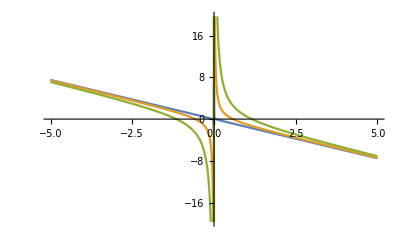

```mathematica
Plot[1/2(c^2/x-3x)/.c->{0.1,1,2}//Evaluate,
{x,-5,5}]
```

```mathematica
Solve[{A y+B x==p,C y+D x==q},{x,y}]//Simplify
```

{{x→(C p-A q)/(B C-A D),y→(D p-B q)/(-B C+A D)}}